```mathematica
Clear["Global`*"];
startTime=SessionTime[];

TOL = 10^-8;
plutoRadius = 1195000`64; (* radius in meters *)

(* physical constants with increased arbitrary precision in mks units*)

NAvagadro = 6.02214129`64*10^23;  (* Avagadro's number *)
R = 8.3144621`64; (*J/mol K; universal gas constant*)
k = 1.3806488`64*10^-23; (* m^2kgs^-2K^-1; Boltzmann constant *)
G = 6.67384`64*10^-11; (* universal gravitational constant *)

αN2 =  1.71`64*10^-30;  (* m^3, mean polarizability of Subscript[N, 2] gas http://cccbdb.nist.gov/exp2.asp?casno=7727379 *)
μN2 = 0.0280134`64; (* kg; molar mass of Subscript[N, 2] *)

(* assumed properties of Pluto *)
p0 = 0.3`64; (* N/m^2; assumed surface pressure of Pluto == 3 microbars *)
T = 50.`64; (* K; assumed atmospheric temperature for isothermal model *)
MPluto = 1.29`64*10^22; (* kg; mass of Pluto *)

distToObserver = 
  5`64*10^12;(* TODO - average Pluto distance from Earth in m = 5*10^12 *)

(* make the atmosphere *)
layers = 100;
atmMin = plutoRadius;
atmMax = 1500000`64;
atmStep = (atmMax - atmMin)/layers;


(*local gravity as a function of r*)
Gravity[r_,M_]:=G*M/r^2;

(*barometric formula-pressure as a function of height*)
Barometric[p0_,M_,h_,T_,r0_,Mplanet_]:=p0 E^((-M Gravity[h+r0,Mplanet] h)/(R T));

SetAtmProperty[startValue_,stopValue_,numShells_]:=Module[{},
If[
startValue==stopValue, (* no variation *)
ConstantArray[startValue,numShells],

(* linear variation *)
Range[startValue,stopValue,(stopValue-startValue)/(numShells-1)]
]
];
```

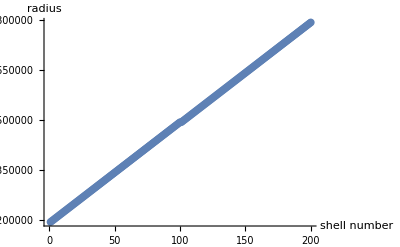

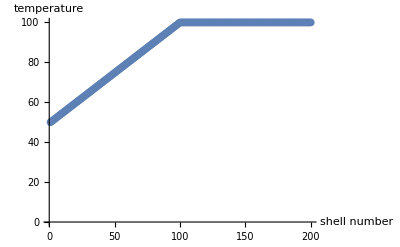

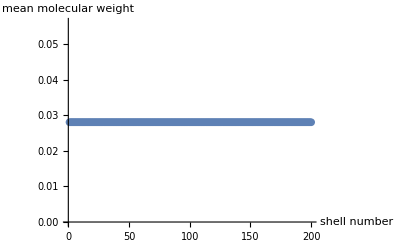

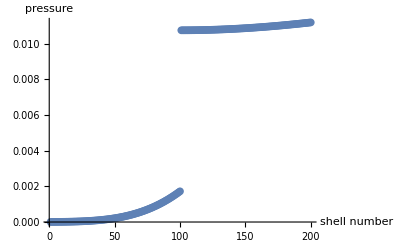

-Graphics-

```mathematica
MakeAtmosphereSection[r0_,r1_,MPlanet_,sectionShells_,T0_,T1_,M0_,M1_,nDens0_]:=Module[{radii,temps,mmw,P0,pressures,nDens},
radii = SetAtmProperty[r0,r1,sectionShells];
temps = SetAtmProperty[T0,T1,sectionShells];
mmw = SetAtmProperty[M0,M1,sectionShells];
P0=nDens0 k T0;
pressures={};
nDens = {nDens0};

Do[
AppendTo[pressures,Barometric[P0,mmw[[i]],radii[[i]],N[temps[[i]]],r0,MPlanet]];
AppendTo[nDens,pressures[[i]]/(k temps[[i]])],
{i,1,Length[radii]}
];
Return[{radii,temps,mmw,pressures,nDens}];
];

(* joins several atmosphere sections consecutively (no additional ordering or continuity assumptions *)
(* takes a list of atmosphere sections (list of lists) as an argument *)
JoinAtmosphereSections[sections_]:=Module[{radii,temps,mmw,pressures,nDens},
radii = {};
temps = {};
mmw = {};
pressures = {};
nDens = {};
Do[
radii= Join[radii,sections[[i,1]]];
temps=Join[temps,sections[[i,2]]];
mmw=Join[mmw,sections[[i,3]]];
pressures=Join[pressures,sections[[i,4]]];
nDens=Join[nDens,sections[[i,5]]];,
{i,1,Length[sections]}
];
Return[{radii,temps,mmw,pressures,nDens}];
];

MakeAtmosphere[boundaryR_,boundaryT_,boundaryM_,sectionShells_,nDensRef_,MPlanet_]:=Module[{numSections,atmosphere,atmSections,section},
numSections = Length[sectionShells];
atmosphere = {};
atmSections = {};
(* check that number of parameters is right *)
If[
Length[boundaryR]≠ numSections+1 || Length[boundaryT]≠ numSections+1||Length[boundaryM]≠ numSections+1 ,
Print["invalid number of arguments in MakeAtmosphere"];
Return[];
];
Do[
(*Print[MakeAtmosphereSection[boundaryR[[i]],boundaryR[[i+1]],MPlanet,sectionShells[[i]],boundaryT[[i]], boundaryT[[i+1]],boundaryM[[i]],boundaryM[[i+1]],nDensRef]];*)
section = MakeAtmosphereSection[boundaryR[[i]],boundaryR[[i+1]],MPlanet,sectionShells[[i]],boundaryT[[i]], boundaryT[[i+1]],boundaryM[[i]],boundaryM[[i+1]],nDensRef];
AppendTo[atmSections,section];,
(*atmSections = Join[atmSections,section];,*)
{i,1,numSections}
];
(*Print[atmSections];*)
Return[JoinAtmosphereSections[atmSections]];
];

r0=plutoRadius;
r1=1.25`64*plutoRadius;
r2 = 1.5`64*plutoRadius;
MPlanet=MPluto;
sectionShells=100;
T0=50;
T1=100;
T2 = 100;
M0=μN2;
M1=μN2;
M2=μN2;
nDens0=10^21;

(*Barometric[nDens0 k T0,μN2,r0,T0,MPlanet,r0]
Barometric[(nDens0 k T1)/2,μN2,(r1+r0)/2,(T1+T0)/2,MPlanet,(r0+r1)/2]
*)

b=MakeAtmosphere[{r0,r1,r2},{T0,T1,T2},{M0,M1,M2},{100,100},nDens0,MPluto];
ListPlot[b[[1]],AxesLabel->{"shell number","radius"}]
ListPlot[b[[2]],AxesLabel->{"shell number","temperature"}]
ListPlot[b[[3]],AxesLabel->{"shell number","mean molecular weight"}]
ListPlot[b[[4]],AxesLabel->{"shell number","pressure"}]
ListPlot[b[[5]],AxesLabel->{"shell number","number density"}]
```